# QuantileRegression scratch pad

### Basic Examples

Text about the example:

```mathematica
SeedRandom[23];
data=Sort@RandomReal[{0,100},100];
data=Map[{#,Sin[#/10]+RandomReal[{-0.6,0.6}]}&,data];
probs={0.25,0.5,0.75};
qFuncs=QuantileRegression[data,12,probs];
```

```mathematica
Simplify/@Through[qFuncs[x]]
```

{Piecewise[{{-1.52316, x>96.9173||x<0.299124}, {-3246.42+108.35 x-1.20289 x^2+0.00444249 x^3, 88.8658≤x≤96.9173}, {354.742-14.0646 x+0.185071 x^2-0.000806755 x^3, x==80.8143}, {286.935-11.5475 x+0.153924 x^2-0.000678284 x^3, 72.7628<x<80.8143}, {388.75-15.7453 x+0.211616 x^2-0.000942575 x^3, x==72.7628}, {103.937-4.75419 x+0.0698637 x^2-0.000331561 x^3, 80.8143<x<88.8658}, {-117.567+5.1301 x-0.0752807 x^2+0.000371726 x^3, 64.7112≤x<72.7628}, {58.5771-3.39772 x+0.0628878 x^2-0.00037756 x^3, 48.6082<x<56.6597}, {3.65502-0.489724 x+0.0115639 x^2-0.0000756182 x^3, 56.6597≤x<64.7112}, {99.955-5.95148 x+0.115425 x^2-0.00073784 x^3, x==48.6082}, {43.9282-2.96315 x+0.0655245 x^2-0.000490793 x^3, x==40.5567}, {-10.6104+1.0711 x-0.0339473 x^2+0.000326761 x^3, 32.5052≤x<40.5567}, {7.09399-0.562888 x+0.0163213 x^2-0.000188732 x^3, 24.4537≤x<32.5052}, {-8.40358+1.33837 x-0.0614281 x^2+0.000871086 x^3, 16.4022≤x<24.4537}, {5.60749-0.128543 x-0.00436786 x^2+0.0000836488 x^3, 40.5567<x<48.6082}, {1.82588-0.532628 x+0.0526421 x^2-0.00144711 x^3, 8.35064≤x<16.4022}, {-0.546351+0.319606 x-0.049414 x^2+0.00262668 x^3, True}}],Piecewise[{{-1.52316, x>96.9173||x<0.299124}, {29.9598-2.25698 x+0.056802 x^2-0.000490223 x^3, 32.5052<x≤40.5567}, {-3518.89+116.672 x-1.28642 x^2+0.00471724 x^3, x==88.8658}, {-4054.91+134.768 x-1.49005 x^2+0.00548104 x^3, 88.8658<x≤96.9173}, {-112.687+4.09716 x-0.0494915 x^2+0.000200764 x^3, 72.7628<x<80.8143}, {832.725-30.9986 x+0.384785 x^2-0.00159049 x^3, x==80.8143}, {605.054-22.5469 x+0.280204 x^2-0.00115912 x^3, 80.8143<x<88.8658}, {210.069-9.21006 x+0.133393 x^2-0.00063705 x^3, 64.7112≤x<72.7628}, {80.457-3.86616 x+0.0599507 x^2-0.000300601 x^3, x==72.7628}, {-226.441+11.0265 x-0.179327 x^2+0.000973802 x^3, 56.6597≤x<64.7112}, {188.605-10.9492 x+0.208527 x^2-0.00130797 x^3, 48.6082<x<56.6597}, {229.119-13.4497 x+0.259968 x^2-0.00166073 x^3, x==48.6082}, {-8.3852+0.95988 x-0.02899 x^2+0.000209996 x^3, x==24.4537}, {-59.7348+4.37777 x-0.10679 x^2+0.00085433 x^3, 40.5567<x<48.6082}, {56.4186-4.69894 x+0.131927 x^2-0.00126062 x^3, x==32.5052}, {-18.9853+2.26031 x-0.0821694 x^2+0.000934897 x^3, 24.4537<x<32.5052}, {3.30261-0.473993 x+0.0296463 x^2-0.000589288 x^3, 16.4022≤x<24.4537}, {-1.67055+0.435613 x-0.0258102 x^2+0.000537728 x^3, 8.35064≤x<16.4022}, {-0.457349-0.000235897 x+0.0263833 x^2-0.00154568 x^3, True}}],Piecewise[{{-1.52316, x>96.9173||x<0.299124}, {-10.0678+0.303872 x-0.0027636 x^2+9.09213×10^-6 x^3, 72.7628<x<80.8143}, {-4350.63+144.56 x-1.59789 x^2+0.00587618 x^3, 88.8658≤x≤96.9173}, {1009.24-37.5351 x+0.465458 x^2-0.00192217 x^3, x==80.8143}, {666.789-24.8225 x+0.308151 x^2-0.00127333 x^3, 80.8143<x<88.8658}, {178.932-7.48857 x+0.10433 x^2-0.000481515 x^3, x==72.7628}, {-52.88+2.32377 x-0.0344604 x^2+0.000174577 x^3, 56.6597<x<64.7112}, {33.1563-1.66486 x+0.0271768 x^2-0.000142922 x^3, x==64.7112}, {111.05-6.35594 x+0.11873 x^2-0.000726651 x^3, 48.6082<x<56.6597}, {183.051-10.7997 x+0.21015 x^2-0.00135357 x^3, x==48.6082}, {2.84928-0.626966 x+0.0176177 x^2-0.000131803 x^3, x==56.6597}, {41.188-2.74566 x+0.0617522 x^2-0.000478078 x^3, x==40.5567}, {-3.21954+0.0215201 x+0.00111684 x^2-8.68454×10^-6 x^3, 64.7112<x<72.7628}, {-3.35864+0.490855 x-0.0162463 x^2+0.000144492 x^3, 24.4537<x<32.5052}, {-16.0617+1.48913 x-0.0426643 x^2+0.000380116 x^3, 40.5567<x<48.6082}, {-6.55839+0.786169 x-0.0253314 x^2+0.000237658 x^3, 32.5052<x<40.5567}, {22.8308-1.92625 x+0.0581143 x^2-0.000618059 x^3, x==32.5052}, {2.45658-0.222563 x+0.012928 x^2-0.000253189 x^3, 16.4022≤x≤24.4537}, {-2.79143+0.737314 x-0.0455934 x^2+0.000936114 x^3, 8.35064≤x<16.4022}, {-0.22916-0.183192 x+0.0646384 x^2-0.00346402 x^3, True}}]}

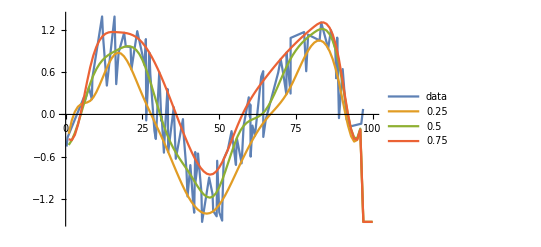

```mathematica
ListPlot[Prepend[Map[#/@Range[Length[data]]&,qFuncs],data],PlotLegends->Prepend[probs,"data"],Joined->{True,True,True,True}]
```

### Applications

#### Fit to a financial time series

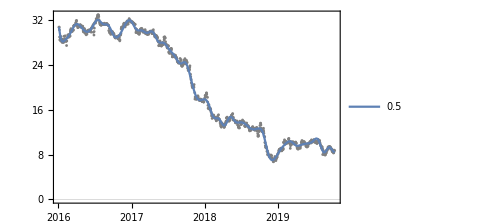
Plot: -Graphics-

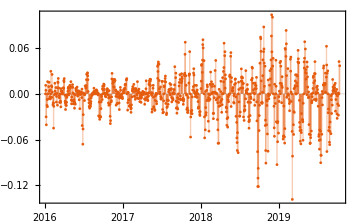
Relative error plots: {0.5→-Graphics-}

```mathematica
QRMonUnit[fdata]⟹
QRMonQuantileRegression[50,0.5]⟹
QRMonDateListPlot⟹
QRMonErrorPlots[DateListPlot->True];
```

### Neat Examples

```mathematica
mnData=Select[RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,40}}],1600],-2<#⟦1⟧<2&];
```

```mathematica
mnData=Join[tempData,{#⟦1⟧,-#⟦2⟧}&/@tempData];
```

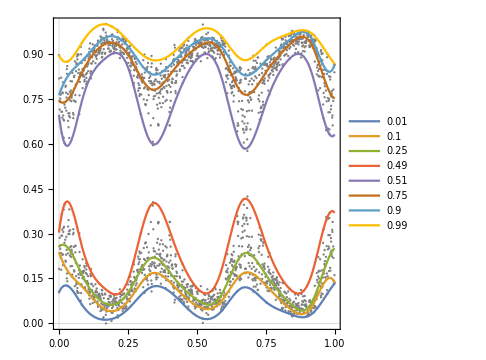
Plot: -Graphics-

```mathematica
QRMonUnit[mnData]⟹
QRMonRescale[Axes->{True,True}]⟹
QRMonQuantileRegression[12,{0.01,0.1,0.25,0.49,0.51,0.75,0.9,0.99}]⟹
QRMonPlot[AspectRatio->Automatic];
```

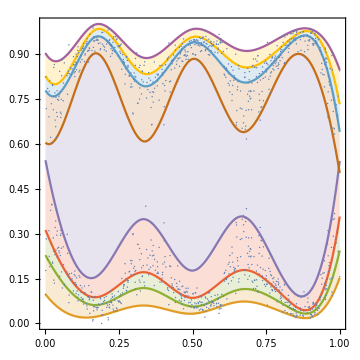

```mathematica
Block[{tempData=RandomSample[tempData,800],data,probs},
data=Join[tempData,{#⟦1⟧,-#⟦2⟧}&/@tempData];
data=SortBy[Transpose[Rescale/@Transpose[data]],#⟦1⟧&];
probs={0.01,0.1,0.25,0.49,0.51,0.75,0.9,0.99};
qFuncs=QuantileRegression[data,6,probs];ListPlot[Prepend[(Transpose[{data⟦All,1⟧,#1/@data⟦All,1⟧}]&)/@qFuncs,data],Joined->Prepend[Table[True,Length[probs]],False],Filling->Prepend[Table[(i+1)->{i+2},{i,Length[probs]-1}],1->None],Frame->True,FrameTicks->False,Axes->False,ImageSize->Medium,AspectRatio->1]
]
```

LinearProgramming::lpipcv: Warning: the interior point algorithm cannot converge to the tolerance of 1.49012×10^-8. The best residual achieved is 2.03116×10^-8, and the solution at that residual has been returned. Setting the option Method -> RevisedSimplex should give a more definite answer, though large problems may take longer computing time.

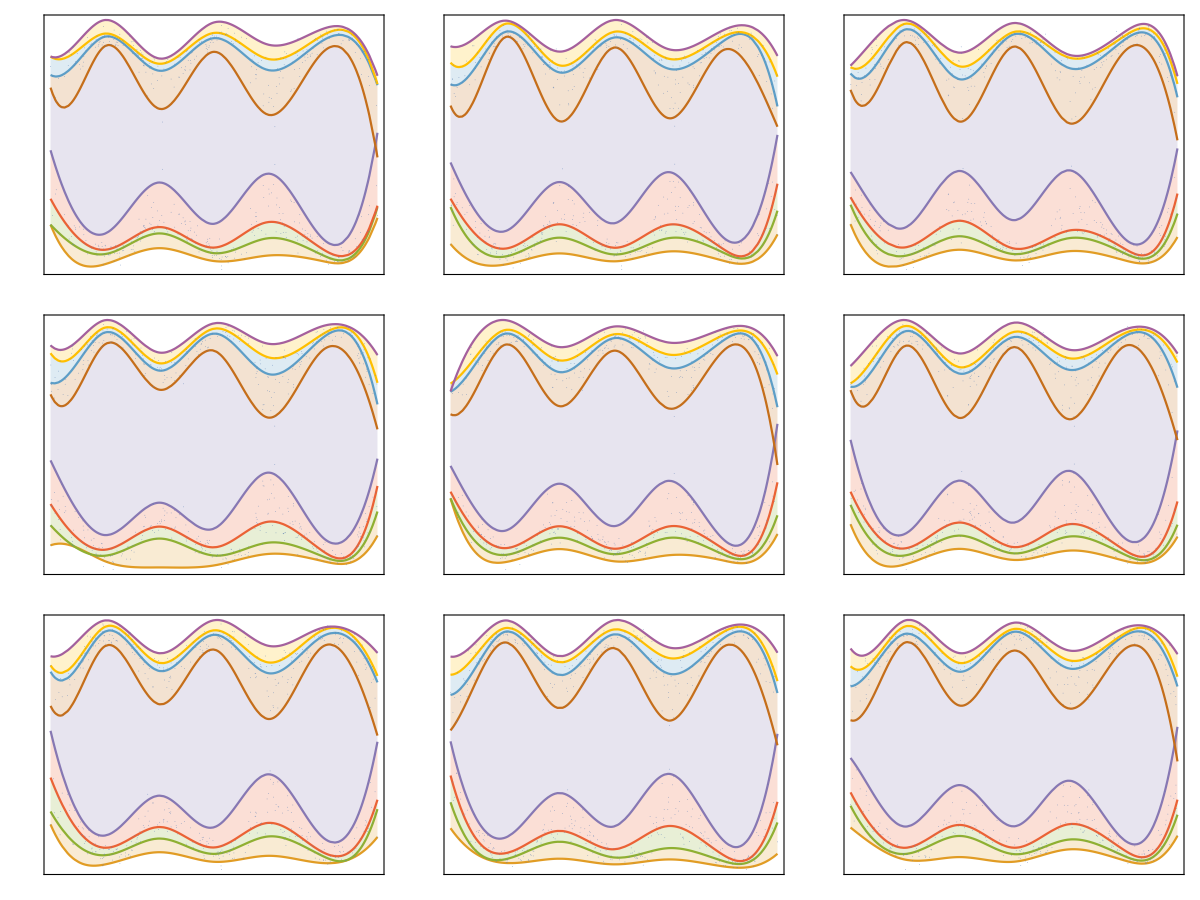

```mathematica
Grid[Table[Block[{tempData=RandomSample[tempData,300],data,probs},
data=Join[tempData,{#⟦1⟧,-#⟦2⟧}&/@tempData];
data=SortBy[Transpose[Rescale/@Transpose[data]],#⟦1⟧&];
probs={0.01,0.1,0.25,0.49,0.51,0.75,0.9,0.99};
qFuncs=QuantileRegression[data,6,probs];ListPlot[Prepend[(Transpose[{data⟦All,1⟧,#1/@data⟦All,1⟧}]&)/@qFuncs,data],Joined->Prepend[Table[True,Length[probs]],False],Filling->Prepend[Table[(i+1)->{i+2},{i,Length[probs]-1}],1->None],Frame->True,FrameTicks->False,Axes->False,ImageSize->Small,AspectRatio->1]
],3,3]]
```

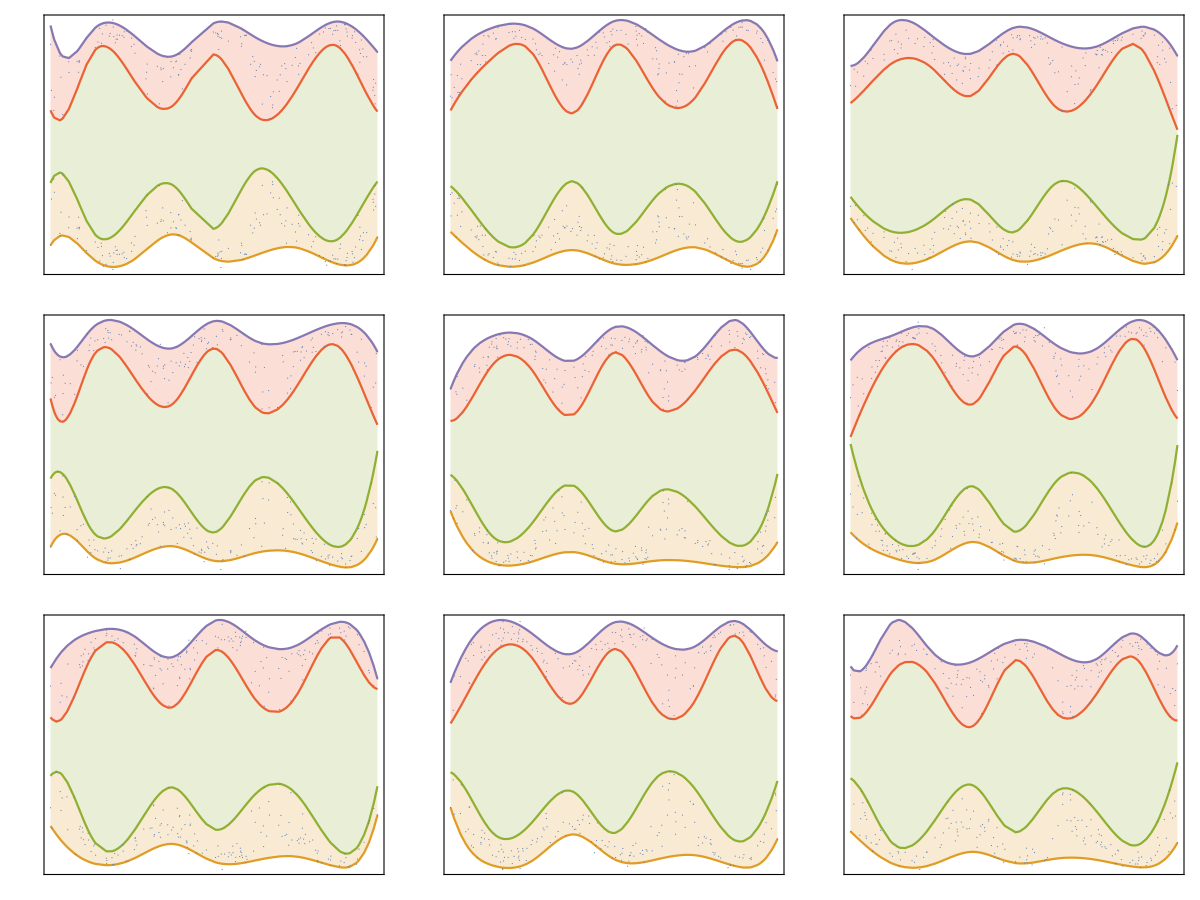

```mathematica
SeedRandom[20];
Grid[Table[Block[{tempData=RandomSample[tempData,160],data,probs},
data=Join[tempData,{#⟦1⟧,-#⟦2⟧}&/@tempData];
data=SortBy[Transpose[Rescale/@Transpose[data]],#⟦1⟧&];
probs={0.02,0.49,0.51,0.98};
qFuncs=QuantileRegression[data,8,probs,Method->{LinearProgramming,Method->"InteriorPoint",Tolerance->10^(-2)}];ListPlot[Prepend[(Transpose[{data⟦All,1⟧,#1/@data⟦All,1⟧}]&)/@qFuncs,data],Joined->Prepend[Table[True,Length[probs]],False],Filling->Prepend[Table[(i+1)->{i+2},{i,Length[probs]-1}],1->None],Frame->True,FrameTicks->False,Axes->False,ImageSize->Small,AspectRatio->1]
],3,3]]
```

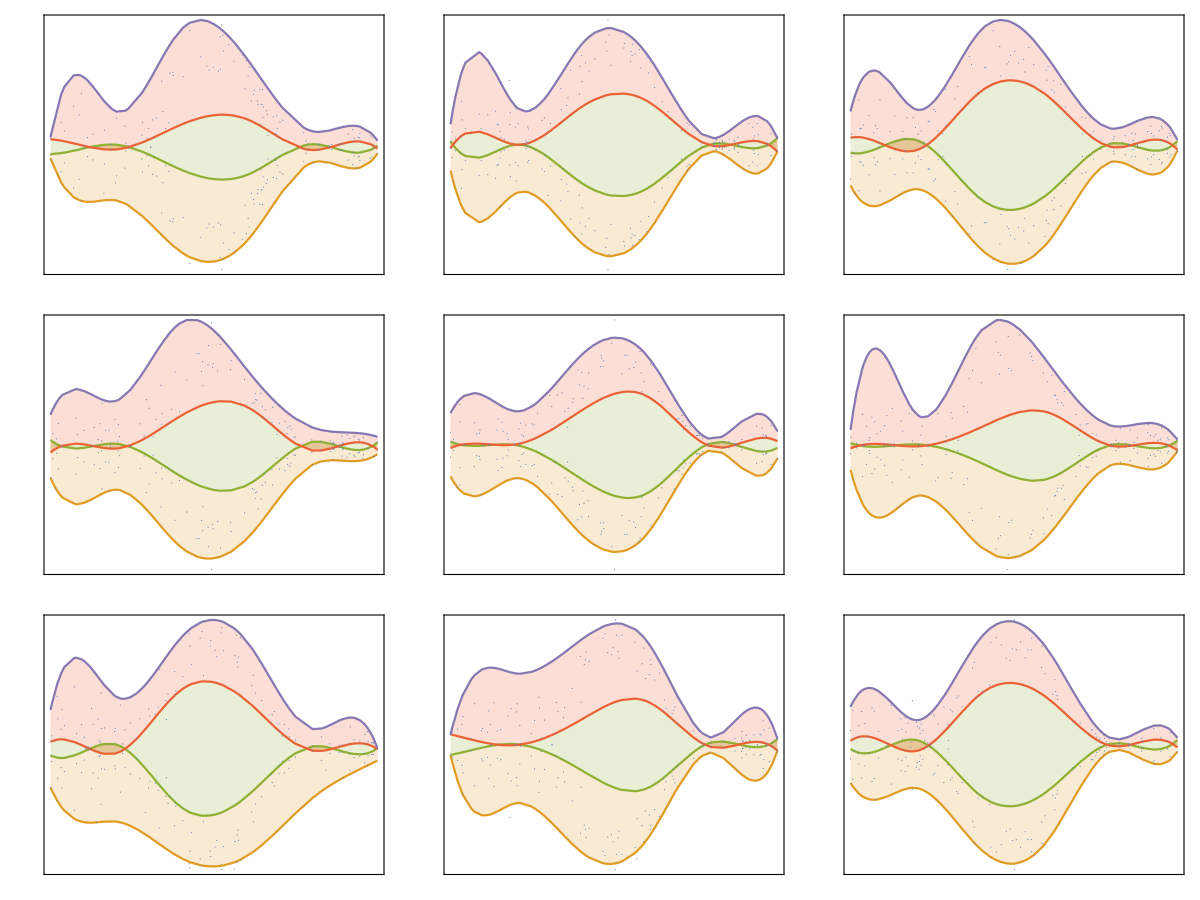

```mathematica
SeedRandom[20];
distData=Table[{x,Exp[-x^2]+RandomVariate[NormalDistribution[0,.15 √(Abs[1.5-x]/1.5)]]},{x,-3,3,.01}];
Grid[Table[Block[{tempData=RandomSample[distData,100],data,probs},
data=Join[tempData,{#⟦1⟧,-#⟦2⟧}&/@tempData];
data=SortBy[Transpose[Rescale/@Transpose[data]],#⟦1⟧&];
probs={0.02,0.48,0.52,0.98};
qFuncs=QuantileRegression[data,5,probs,Method->{LinearProgramming,Method->"InteriorPoint",Tolerance->10^(-2)}];ListPlot[Prepend[(Transpose[{data⟦All,1⟧,#1/@data⟦All,1⟧}]&)/@qFuncs,data],Joined->Prepend[Table[True,Length[probs]],False],Filling->Prepend[Table[(i+1)->{i+2},{i,Length[probs]-1}],1->None],Frame->True,FrameTicks->False,Axes->False,ImageSize->Small,AspectRatio->1]
],3,3]]
```